```mathematica
**STEADY STATE**
```

```mathematica
a=.3;b=.99;
kss=(a b)^(1/(1-a))
css=(a b)^(a/(1-a))-(a b)^(1/(1-a))
```

0.17652

0.417824

```mathematica
**POLICY RULE IN (B)**
```

```mathematica
g=1-b a;
prcb=(1-a b) (k^a);
prkb=a b (k^a);
```

```mathematica
**POLICY RULE IN (C)**
```

```mathematica
a=.;b=.;
S=(n^2)-n (((1+b)/b)-b c a (a-1) (k^(a-2)))+(1/b)
FullSimplify[Solve[S==0,n]]
```

1/b-((1+b)/b-(-1+a) a b c k^(-2+a)) n+n^2

{{n→-(-(1+b) k^2+(-1+a) a b^2 c k^a+√(-4 b k^4+((1+b) k^2-(-1+a) a b^2 c k^a)^2))/(2 b k^2)},{n→((1+b) k^2-(-1+a) a b^2 c k^a+√(-4 b k^4+((1+b) k^2-(-1+a) a b^2 c k^a)^2))/(2 b k^2)}}

```mathematica
**in steady state
```

```mathematica
a=.3;b=.99;
k=(a b)^(1/(1-a))
c=(a b)^(a/(1-a))-(a b)^(1/(1-a))
n1=-(-(1+b) k^2+(-1+a) a b^2 c k^a+√(-4 b k^4+((1+b) k^2-(-1+a) a b^2 c k^a)^2))/(2 b k^2)
n2=((1+b) k^2-(-1+a) a b^2 c k^a+√(-4 b k^4+((1+b) k^2-(-1+a) a b^2 c k^a)^2))/(2 b k^2)
```

0.17652

0.417824

0.3

3.367

```mathematica
**the policy rules
```

```mathematica
prkc=n (k-kss)-kss
prcc=k (1/b)+kss (1-(1/b))-n (k-kss)+kss-css
```

```mathematica
**PLOTTING EVERITHING!**
```

```mathematica
a=.3;b=.99;n=.3;

kss=(a b)^(1/(1-a));
css=(a b)^(a/(1-a))-(a b)^(1/(1-a));

prcb=(1-a b) (k^a);
prkb=a b (k^a);
prkc=n (k-kss)+kss;
prcc=((1/b)-n) (k-kss)+css;
```

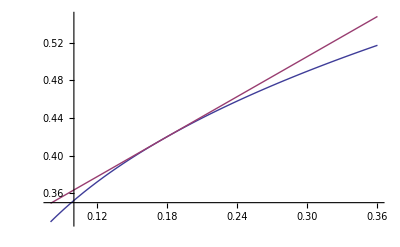

```mathematica
Plot[{prcb,prcc},{k,.08,.36}]
```

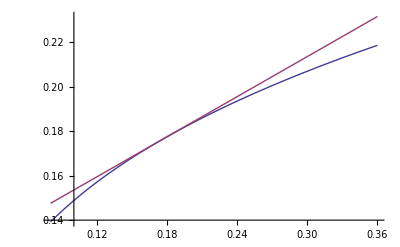

```mathematica
Plot[{prkb,prkc},{k,.08,.36}]
```

```mathematica
**DIFFERENCES ON POLICY RULES**
```

```mathematica
a=.3;b=.99;n=.3;
kss=(a b)^(1/(1-a));
css=(a b)^(a/(1-a))-(a b)^(1/(1-a));
prcb=(1-a b) (k^a);
prcc=((1/b)-n) (k-kss)+css;
dif=(prcc-prcb)/css;
```

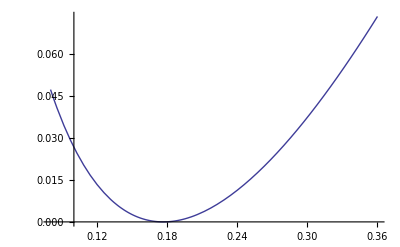

```mathematica
Plot[{dif},{k,.08,.36}]
```

```mathematica
**DERIVATIVES**
```

```mathematica
A=Log[c]
D[A,c]
Integrate[A,c]
```

Log[c]

1/c

-c+c Log[c]